-Graphics-

## Form factors of the twist fields

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Rule1[l_]:={F[ms__][θs__]:>S[{ms}⟦l⟧,{ms}⟦l+1⟧][{θs}⟦l⟧-{θs}⟦l+1⟧]F[Sequence@@ReplacePart[{ms},{l->{ms}⟦l+1⟧,l+1->{ms}⟦l⟧}]]
[Sequence@@ReplacePart[{θs},{l->{θs}⟦l+1⟧,l+1->{θs}⟦l⟧}]]}
Rule2:={F[m1_,ms__][θ1_,θs__]:>F[ms,m1+1][θs,θ1-2π I]}
```

```mathematica
F[Subscript[μ, 1],Subscript[μ, 2],Subscript[μ, 3]][Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]]/.Rule1[1]
```

F(μ_2,μ_1,μ_3)(θ_2,θ_1,θ_3) S(μ_1,μ_2)(θ_1-θ_2)

```mathematica
F[Subscript[μ, 1],Subscript[μ, 2],Subscript[μ, 3]][Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]]/.Rule2
```

F(μ_2,μ_3,μ_1+1)(θ_2,θ_3,θ_1-2 ⅈ π)

-Graphics-

```mathematica
sldif=F[a__][t1_,t2_]:>F[a][t1-t2];
S[a1_?NumericQ,a2_?NumericQ][θ_]:=If[a1==a2,S[θ],1];
S[-θ]=1/S[θ];
```

```mathematica
{F[1,1][θ,0],F[1,1][θ,0]/.Rule2/.Rule2}/.sldif
```

{F(1,1)(θ),F(2,2)(θ)}

```mathematica
{F[1,3][θ,0],F[1,3][θ,0]/.Rule2/.Rule2}/.sldif
```

{F(1,3)(θ),F(2,4)(θ)}

```mathematica
Grid@{{F[1,1][θ,0],"=",F[1,1][θ,0]/.Rule2}}/.sldif
Grid@{{F[1,1][θ,0],"=",F[1,1][θ,0]/.Rule2/.Rule1[1]/.Rule2}}/.sldif
```

F(1,1)(θ) | = | F(1,2)(-θ+2 ⅈ π)

F(1,1)(θ) | = | F(1,3)(-θ+4 ⅈ π)

```mathematica
F[1,1][θ,0]/.Rule1[1]/.sldif
```

```mathematica
{{F[1,1][θ], "=", S[θ] F[1,1][-θ]}}
```

F(1,1)(θ) | = | S(θ) F(1,1)(-θ)

-Graphics-

```mathematica
xp=Exp[+(π I)/(2n)];
xm=Exp[-(π I)/(2n)];
f[θ_]=(x (A1+A2 x+A3 x^2))/((x^2-xp^2)(x^2-xm^2))/.x->Exp[θ/(2n)]//FullSimplify;
```

```mathematica
slA12=Solve[Series[{f[θ]+f[-θ],f[θ]+f[θ+2π I n]},{θ,0,3}]==0//LogicalExpand,{A1,A2}][[1]]
```

{A1→-A3,A2→0}

```mathematica
f[θ]/.slA12//FullSimplify
```

-(A3 sinh(θ/(2 n)))/(cos(π/n)-cosh(θ/n))

```mathematica
slA3=Solve[Residue[f[θ+I π]/.slA12,{θ,0}]==F0,A3][[1]]
```

{A3→(F0 ⅇ^(-(ⅈ π)/(2 n)) (1+ⅇ^((ⅈ π)/n)))/n}

```mathematica
F211=f[θ]/.slA12/.slA3//FullSimplify
```

(F0 cos(π/(2 n)) csc((π-ⅈ θ)/(2 n)) csc((π+ⅈ θ)/(2 n)) sinh(θ/(2 n)))/n

-Graphics-

-Graphics-

```mathematica
Clear[F2];
F2[1,1][θ_]=F211;
F2[1,j_][θ_]=F2[1,1][-θ+2π I(j-1)];
```

```mathematica
tn=n (F2[1,j][θ1-θ2]//Abs)^2 Exp[-r m(Cosh[θ1]+Cosh[θ2])]/.θ1->θp+θ/2/.θ2->θp-θ/2//ComplexExpand//FullSimplify
```

(2 F0^2 cos^2(π/(2 n)) (cos((2 π (j-1))/n)-cosh(θ/n)) ⅇ^(-2 m r cosh(θ/2) cosh(θp)))/(n (cos((π (3-2 j))/n)-cosh(θ/n)) (cosh(θ/n)-cos((π (2 j-1))/n)))

```mathematica
int=Simplify[Integrate[tn Dt[θp]/Dt[x]/.θp->Log[x],{x,0,∞},GenerateConditions->False],θ>0&&r>0&&m>0]
```

(4 F0^2 cos^2(π/(2 n)) (cos((2 π (j-1))/n)-cosh(θ/n)) 02 m r cosh(θ/2))/(n (cos((π (3-2 j))/n)-cosh(θ/n)) (cosh(θ/n)-cos((π-2 π j)/n)))

-Graphics-

```mathematica
ts=(4  Cos[π/(2 n)]^2 (Cos[(2 π (j-1))/n]-Cosh[θ/n]))/(n (Cos[(π (3-2 j))/n]-Cosh[θ/n]) (Cosh[θ/n]-Cos[(π-2 π j)/n]))/.θ->1/2;
```

```mathematica
sum[n0_]:=Sum[ts/.n->n0,{j,n0}]
p1=ListPlot[Table[{n0,sum[n0]},{n0,1,4}],PlotStyle->Red];
```

```mathematica
ft[k_,n0_]:=ft[k,n0]=NIntegrate[ts Exp[-2π I j k]/.n->n0,{j,0,n0}]
```

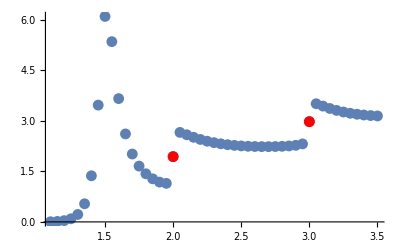

```mathematica
Dynamic[n//N]
p2=Table[{n,Sum[ft[k,n],{k,-20,20}]},{n,1+1/10,3+1/2,1/20}]//Re//ListPlot;
Show[p2,p1]
```

-Graphics-

```mathematica
(*representation by poles*)
sing=F0^2((4  Sin[π/(2 n)] Cos[π/(2 n)]^2 Csc[π/n] Sin[π/(2 n)+(ⅈ θ)/n] Csc[π/n+(ⅈ θ)/n] Csch[θ/n](1/(θ-(2π I(j-1)+I π+2 π I n l))+1/(θ+(2π I(j-1)-I π+2 π I n l)))+4 Sin[π/(2 n)] Cos[π/(2 n)]^2 Csc[π/n] Sin[π/(2 n)-(ⅈ θ)/n] Csc[π/n-(ⅈ θ)/n] Csch[θ/n](1/(θ+(2π I(j-1)+I π+2 π I n l))+1/(θ-(2π I(j-1)-I π+2 π I n l)))))
```

```mathematica
tosuminn/Sum[sing,{l,-∞,∞}]/.F0->1//FullSimplify
```

1

-Graphics-

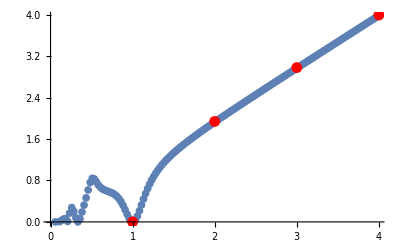

```mathematica
summed1=Collect[Sum[sing,{j,1,n}],1/Sin[_],Simplify]
summed2=Collect[Sum[sing/.j->n-j+1,{j,1,n}],1/Sin[_],Simplify]
summedImproved[l_,n_]=If[l≥0,summed1,summed2]
p3=Table[{n,Sum[summedImproved[l,n],{l,-20,20}]}/.θ->1/2//N,{n,1+1/100,4,1/100}]//ListPlot;
Show[p3,p1]
```

-Graphics-